# Omicron US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Vermont","Utah","Minnesota","New Mexico","Washington","Michigan"};
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01","2022-01-15","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Rt estimates

Using GARW (growth autoregressive random walk) model

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,median_freq,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,median_freq→5,R_upper_95→6,R_lower_95→7,R_upper_80→8,R_lower_80→9,R_upper_50→10,R_lower_50→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=First[Sort[rtData[[All,1]]]]
```

2021-10-15

```mathematica
startDate="2021-11-01";
```

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-19

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-01-19

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
states=Union[rtData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Nebraska,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Virginia,Wisconsin}

```mathematica
Length[states]
```

25

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[5]]>0.001];
```

```mathematica
rtData=DeleteCases[rtData,x_/;x[[2]]=="South Africa"&&x[[5]]<0.01];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{35,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
variantsCountryRtLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rtGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{30,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,10]},
{0,7}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.1],{2,1}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[variantsCountryRtLabelPlot[country,variants[[2;;3]]],Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryRtPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

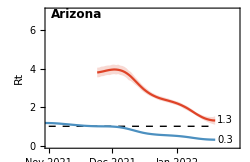
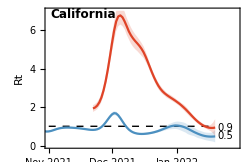
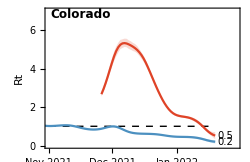
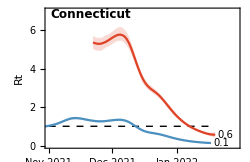
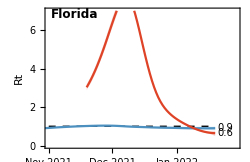
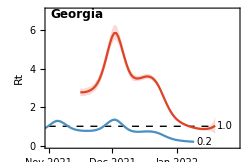
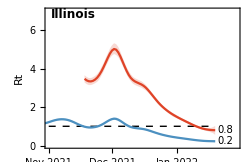
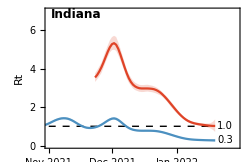
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-rt.png

Rt

```mathematica
Map[#->{rtGather[#,"Omicron"][[-1,1]],Round[rtGather[#,"Omicron"][[-1,2]],0.1],Round[rtGatherLower[#,"Omicron"][[-1,2]],0.1],Round[rtGatherUpper[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-19,1.3,1.1,1.5},California→{2022-01-19,0.9,0.5,1.4},Colorado→{2022-01-19,0.5,0.3,0.7},Connecticut→{2022-01-19,0.6,0.4,0.7},Florida→{2022-01-19,0.6,0.5,0.8},Georgia→{2022-01-19,1.,0.6,1.5},Illinois→{2022-01-19,0.8,0.6,1.},Indiana→{2022-01-19,1.,0.7,1.4},Louisiana→{2022-01-19,1.1,0.6,1.5},Maryland→{2022-01-19,0.4,0.3,0.5},Massachusetts→{2022-01-19,1.3,1.,1.6},Nebraska→{2022-01-19,1.1,0.8,1.4},Nevada→{2022-01-19,1.6,1.3,2.},New Jersey→{2022-01-19,0.5,0.3,0.6},New York→{2022-01-19,0.5,0.4,0.6},North Carolina→{2022-01-19,1.,0.8,1.2},North Dakota→{2022-01-19,1.,0.8,1.2},Ohio→{2022-01-19,0.3,0.2,0.4},Oregon→{2022-01-19,1.5,1.,1.9},Pennsylvania→{2022-01-19,0.6,0.4,0.7},South Carolina→{2022-01-19,1.,0.7,1.2},Tennessee→{2022-01-19,0.8,0.6,1.},Texas→{2022-01-19,0.5,0.1,0.9},Virginia→{2022-01-19,0.7,0.5,0.9},Wisconsin→{2022-01-19,1.,0.7,1.3}}

## Little r estimates

Using fixed growth model

```mathematica
rData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_little-r-combined-"<>model<>".tsv"];
```

```mathematica
header=rData[[1]]
```

{date,location,variant,median_r,median_freq,r_upper_95,r_lower_95,r_upper_80,r_lower_80,r_upper_50,r_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_r→4,median_freq→5,r_upper_95→6,r_lower_95→7,r_upper_80→8,r_lower_80→9,r_upper_50→10,r_lower_50→11}

```mathematica
rData=Drop[rData,1];
```

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rData=Cases[rData,x_/;x[[5]]>0.001];
```

```mathematica
rGather[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rGatherLower[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,9}]]
```

```mathematica
rGatherUpper[country_,variant_]:=Cases[rData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
variantCountryLittleRPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rGather[country,variant];
lowerSeries=rGatherLower[country,variant];
upperSeries=rGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,5},{15,10}},Joined->True,PlotRange->{{startDate,DatePlus[modelEndDate,7]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,0}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
variantsCountryLittleRLabelPlot[country_,variants_]:=Module[{medians,finalDates,finalValues},
medians=Map[Last[rGather[country,#]]&,variants];
finalDates=medians[[All,1]];
finalValues=medians[[All,2]];
DateListPlot[{},Frame->{True,True,False,False},FrameLabel->{"","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{42,5},{15,10}},PlotRange->{{startDate,DatePlus[modelEndDate,15]},
{-0.35,0.5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Prolog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],MapThread[Text[Style[NumberForm[Round[#2,0.01],{2,2}],Black,FontSize->10,FontFamily->"Helvetica"],{DatePlus[#1,1],#2},{-1,0}]&,{finalDates,finalValues}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryLittleRPlot[country_]:=Show[variantsCountryLittleRLabelPlot[country,variants[[2;;3]]],Table[variantCountryLittleRPlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryLittleRPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

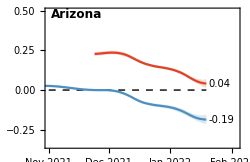
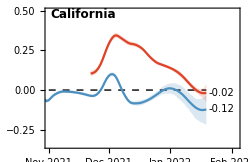
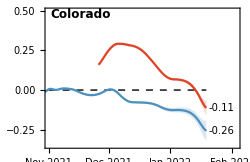
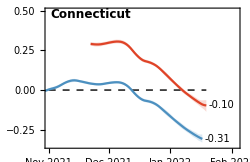
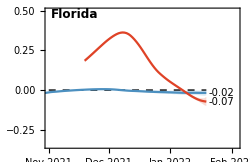
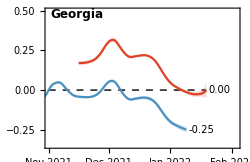
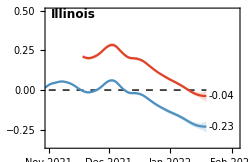
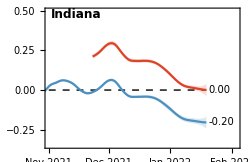
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-little-r.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-little-r.png

Little r

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[rGather[#,"Omicron"][[-1,2]],0.01],Round[rGatherLower[#,"Omicron"][[-1,2]],0.01],Round[rGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-19,0.04,0.01,0.07},California→{2022-01-19,-0.02,-0.08,0.04},Colorado→{2022-01-19,-0.11,-0.16,-0.07},Connecticut→{2022-01-19,-0.1,-0.14,-0.06},Florida→{2022-01-19,-0.07,-0.1,-0.04},Georgia→{2022-01-19,0.,-0.05,0.05},Illinois→{2022-01-19,-0.04,-0.08,0.},Indiana→{2022-01-19,0.,-0.04,0.04},Louisiana→{2022-01-19,0.02,-0.03,0.07},Maryland→{2022-01-19,-0.13,-0.16,-0.11},Massachusetts→{2022-01-19,0.04,0.01,0.07},Nebraska→{2022-01-19,0.01,-0.03,0.05},Nevada→{2022-01-19,0.08,0.04,0.11},New Jersey→{2022-01-19,-0.13,-0.15,-0.1},New York→{2022-01-19,-0.11,-0.14,-0.08},North Carolina→{2022-01-19,0.01,-0.02,0.03},North Dakota→{2022-01-19,0.,-0.03,0.03},Ohio→{2022-01-19,-0.22,-0.28,-0.17},Oregon→{2022-01-19,0.07,0.03,0.11},Pennsylvania→{2022-01-19,-0.1,-0.13,-0.06},South Carolina→{2022-01-19,0.,-0.04,0.03},Tennessee→{2022-01-19,-0.03,-0.08,0.},Texas→{2022-01-19,-0.09,-0.18,0.},Virginia→{2022-01-19,-0.06,-0.09,-0.03},Wisconsin→{2022-01-19,-0.01,-0.06,0.04}}

Doubling time

```mathematica
Map[#->{rGather[#,"Omicron"][[-1,1]],Round[Log[2]/rGather[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherUpper[#,"Omicron"][[-1,2]],0.1],Round[Log[2]/rGatherLower[#,"Omicron"][[-1,2]],0.1]}&,states]
```

{Arizona→{2022-01-19,16.9,10.2,51.5},California→{2022-01-19,-40.2,18.,-9.1},Colorado→{2022-01-19,-6.1,-9.7,-4.3},Connecticut→{2022-01-19,-7.1,-10.9,-5.1},Florida→{2022-01-19,-9.5,-15.9,-6.9},Georgia→{2022-01-19,-256.5,14.9,-14.},Illinois→{2022-01-19,-18.3,-213.5,-9.1},Indiana→{2022-01-19,1039.1,17.4,-18.},Louisiana→{2022-01-19,38.6,9.9,-20.6},Maryland→{2022-01-19,-5.1,-6.4,-4.2},Massachusetts→{2022-01-19,15.5,9.5,92.9},Nebraska→{2022-01-19,75.,14.8,-20.1},Nevada→{2022-01-19,8.5,6.1,15.7},New Jersey→{2022-01-19,-5.5,-6.9,-4.5},New York→{2022-01-19,-6.1,-8.7,-4.8},North Carolina→{2022-01-19,110.5,21.,-29.9},North Dakota→{2022-01-19,4766.,24.6,-22.3},Ohio→{2022-01-19,-3.1,-4.1,-2.5},Oregon→{2022-01-19,9.6,6.2,20.8},Pennsylvania→{2022-01-19,-7.3,-11.1,-5.4},South Carolina→{2022-01-19,-442.9,21.8,-19.7},Tennessee→{2022-01-19,-19.8,-515.5,-9.},Texas→{2022-01-19,-7.9,-287.3,-3.8},Virginia→{2022-01-19,-11.8,-24.8,-7.5},Wisconsin→{2022-01-19,-96.5,15.9,-12.4}}

## Prevalence

Using fixed growth model

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I,I_upper_95,I_lower_95,I_upper_80,I_lower_80,I_upper_50,I_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I→4,I_upper_95→5,I_lower_95→6,I_upper_80→7,I_lower_80→8,I_upper_50→9,I_lower_50→10}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{20,240000}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

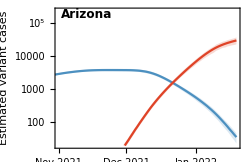
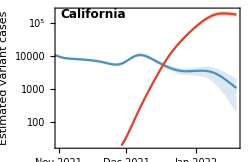
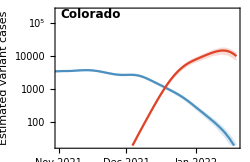
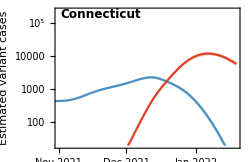
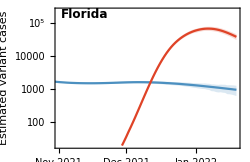
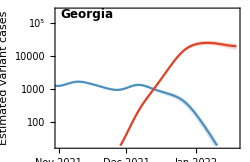
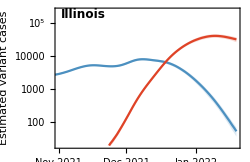
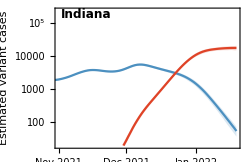
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-log-cases.png

```mathematica
yMaxForCountry[country_]:=Max[Flatten[Table[pGatherUpper[country,variant][[All,2]],{variant,variants}]]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,yMaxForCountry[country]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{modelEndDate,0}}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,2,3}]]
```

```mathematica
panels=Map[countryPrevalencePlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

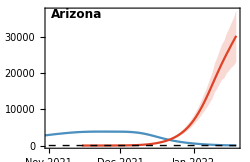
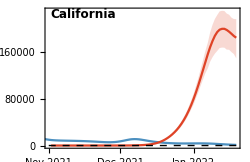
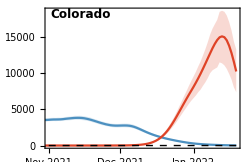
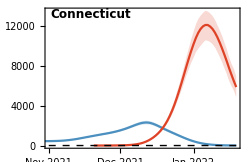
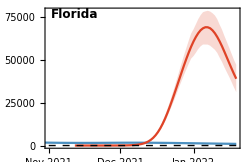
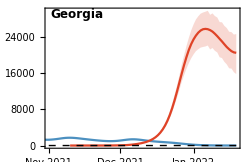
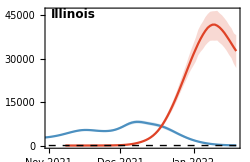
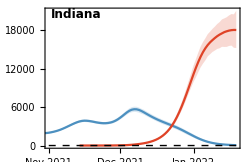
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-cases.png

Prevalence

```mathematica
Map[#->{pGather[#,"Omicron"][[-1,1]],Round[pGather[#,"Omicron"][[-1,2]]],Round[pGatherLower[#,"Omicron"][[-1,2]]],Round[pGatherUpper[#,"Omicron"][[-1,2]]]}&,states]
```

{Arizona→{2022-01-19,30415,23126,37338},California→{2022-01-19,184852,149516,216742},Colorado→{2022-01-19,10219,7357,13252},Connecticut→{2022-01-19,5890,4872,6984},Florida→{2022-01-19,39080,31249,47239},Georgia→{2022-01-19,20418,15735,24541},Illinois→{2022-01-19,32686,26827,38146},Indiana→{2022-01-19,18000,15195,20994},Louisiana→{2022-01-19,20949,17248,25022},Maryland→{2022-01-19,5401,4441,6405},Massachusetts→{2022-01-19,27729,19283,36228},Nebraska→{2022-01-19,6748,5548,8009},Nevada→{2022-01-19,15495,12943,18080},New Jersey→{2022-01-19,10678,9198,12058},New York→{2022-01-19,25858,21080,31181},North Carolina→{2022-01-19,33314,28491,37908},North Dakota→{2022-01-19,2392,1992,2794},Ohio→{2022-01-19,18173,14776,21814},Oregon→{2022-01-19,17679,14725,20534},Pennsylvania→{2022-01-19,18302,16408,20173},South Carolina→{2022-01-19,17240,14886,19839},Tennessee→{2022-01-19,14601,12773,16282},Texas→{2022-01-19,70421,48697,89383},Virginia→{2022-01-19,15643,13510,17650},Wisconsin→{2022-01-19,28933,23090,33599}}

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated Omicron frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,1}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,0},{endDate,0}}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=variantCountryFrequencyPlot[country,variants[[3]],colors[[3]]]
```

```mathematica
panels=Map[countryFrequencyPlot,states];
```

```mathematica
legendPanel=PointLegend[colors[[2;;3]],variants[[2;;3]],LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}];
```

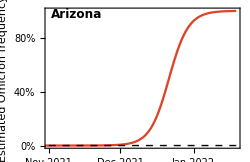
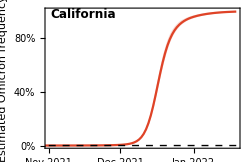
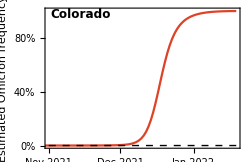
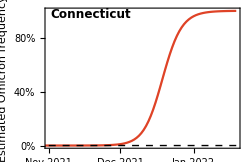
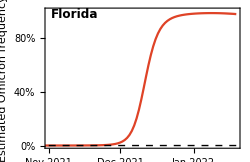
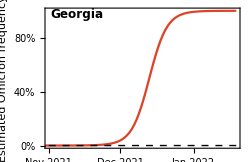
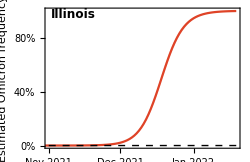
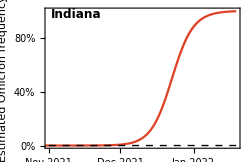
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-estimated-frequency.png

Frequency

```mathematica
Map[#->{fGather[#,"Omicron"][[-1,1]],Round[fGather[#,"Omicron"][[-1,2]],0.01],Round[fGatherLower[#,"Omicron"][[-1,2]],0.01],Round[fGatherUpper[#,"Omicron"][[-1,2]],0.01]}&,states]
```

{Arizona→{2022-01-19,1.,1.,1.},California→{2022-01-19,0.99,0.99,1.},Colorado→{2022-01-19,1.,1.,1.},Connecticut→{2022-01-19,1.,1.,1.},Florida→{2022-01-19,0.98,0.97,0.98},Georgia→{2022-01-19,1.,1.,1.},Illinois→{2022-01-19,1.,1.,1.},Indiana→{2022-01-19,1.,1.,1.},Louisiana→{2022-01-19,1.,1.,1.},Maryland→{2022-01-19,0.97,0.96,0.99},Massachusetts→{2022-01-19,1.,0.99,1.},Nebraska→{2022-01-19,0.99,0.99,1.},Nevada→{2022-01-19,1.,1.,1.},New Jersey→{2022-01-19,1.,1.,1.},New York→{2022-01-19,1.,0.99,1.},North Carolina→{2022-01-19,0.99,0.99,1.},North Dakota→{2022-01-19,0.99,0.99,1.},Ohio→{2022-01-19,1.,1.,1.},Oregon→{2022-01-19,1.,1.,1.},Pennsylvania→{2022-01-19,1.,1.,1.},South Carolina→{2022-01-19,1.,1.,1.},Tennessee→{2022-01-19,1.,1.,1.},Texas→{2022-01-19,1.,1.,1.},Virginia→{2022-01-19,1.,1.,1.},Wisconsin→{2022-01-19,1.,1.,1.}}

## Phase diagrams

Convert to cases per 100k per day

```mathematica
perCapitaPGather[state_,variant_]:=Module[{popSize,stateName},
stateName=StringReplace[state," "->""];
popSize=QuantityMagnitude[AdministrativeDivisionData[{stateName, "UnitedStates"},"Population"]];
Map[{#[[1]],100000*#[[2]]/popSize}&,pGather[state,variant]]
]
```

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
phaseGather[country_,variant_]:=compareWithDate[perCapitaPGather[country,variant],rGather[country,variant]][[All,{2,3}]]
```

```mathematica
countryRPrevalencePhasePlot[country_]:=Module[{pairsOmicron},
pairsOmicron=phaseGather[country,"Omicron"];
ListLogLinearPlot[{pairsOmicron,{Last[pairsOmicron]}},Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,600},
{-0.25,0.45}},Joined->{True,False},PlotMarkers->{None,{"•",Scaled[0.12]}},PlotStyle->{colors[[3]],colors[[3]]},
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
panels=Map[countryRPrevalencePhasePlot,states];
```

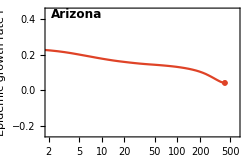
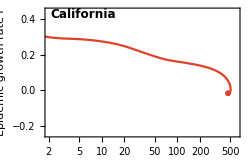
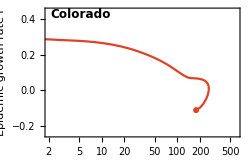
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[panels,gridCount],Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt.png

```mathematica
stateLines=Map[With[{pairs=phaseGather[#,"Omicron"]},pairs]&,states];
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{2,600},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]],Opacity[0.5]]];
```

```mathematica
statePoints=Map[With[{pairs=phaseGather[#,"Omicron"]},Last[pairs]]&,states];
```

```mathematica
figPoints=ListLogLinearPlot[statePoints,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{{2,150},
{-0.25,0.4}},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]}];
```

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

```mathematica
Export["figures/"<>dataset<>"_variant-cases-vs-rt-overlay.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_variant-cases-vs-rt-overlay.png

### Growth rate vs peak incidence

```mathematica
initialR[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,(#1[[1]]-10)^2<(#2[[1]]-10)^2&];
sorted[[1,2]]
]
```

```mathematica
initialR["Washington","Omicron"]
```

0.159261

```mathematica
peakIncidence[state_,variant_]:=Module[{pairs,sorted},
pairs=phaseGather[state,variant];
sorted=Sort[pairs,#1[[1]]>#2[[1]]&];
sorted[[1,1]]
]
```

```mathematica
peakIncidence["Washington","Omicron"]
```

696.065

```mathematica
pairs=Map[{initialR[#,"Omicron"],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Initial epidemic growth rate r","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

```mathematica
rValues=Map[initialR[#,"Omicron"]&,states]
```

{0.177584,0.27724,0.264416,0.264821,0.331846,0.209152,0.212807,0.183619,0.155127,0.24915,0.281708,0.176543,0.216665,0.216049,0.259912,0.237418,0.163695,0.191164,0.184426,0.179078,0.199304,0.18972,0.135264,0.240267,0.222456}

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

```mathematica
baseColorFunction[t_]:=Blend[{Lighter[ColorData["Rainbow"][0.15],0.0],Lighter[ColorData["Rainbow"][0.3],0.0],Lighter[ColorData["Rainbow"][0.7],0.0],Lighter[ColorData["Rainbow"][0.9],0.0]},t]
```

```mathematica
standardizedColorFunction[t_,min_,max_]:=baseColorFunction[(t-min)/(max-min)]
```

```mathematica
phaseColors=Map[standardizedColorFunction[#,Min[rValues],Max[rValues]]&,rValues]
```

{RGBColor[0.28029028047749155, 0.4644802676771136, 0.7648772201532976],RGBColor[0.822443456764128, 0.6575119438919637, 0.2432137471300573],RGBColor[0.7935208611272465, 0.7068616570412029, 0.27038673236695976],RGBColor[0.7966722211864831, 0.7077587383842251, 0.2673225527200817],RGBColor[0.8929546, 0.38966160000000005, 0.17940080000000003],RGBColor[0.3630771670094848, 0.584329480471021, 0.6889224699056763],RGBColor[0.39154689337755283, 0.5924338099940422, 0.6612403407774821],RGBColor[0.28488469231021385, 0.49082375513934307, 0.7615909008410218],RGBColor[0.2631918610018032, 0.3664411681184554, 0.777107483390073],RGBColor[0.6746170707597303, 0.6730139309964802, 0.38600112346546755],RGBColor[0.8282133771779272, 0.6355937747042156, 0.23799193949209674],RGBColor[0.2794979199708092, 0.45993702257124647, 0.7654439846772895],RGBColor[0.4215950258652557, 0.6009874562104974, 0.632023471151414],RGBColor[0.4168020922862847, 0.5996230766374819, 0.6366838112095028],RGBColor[0.7584420800111219, 0.696875962140044, 0.3044950808618497],RGBColor[0.5832395459496662, 0.6470019643732459, 0.47485074599096194],RGBColor[0.26971533985188495, 0.4038455605748065, 0.7724413290902865],RGBColor[0.29062942399642044, 0.5237629588196944, 0.757481773629185],RGBColor[0.28549933321521487, 0.4943479897017188, 0.7611512566929214],RGBColor[0.2814277179059032, 0.47100211850925344, 0.764063626874421],RGBColor[0.2968272409270986, 0.5593000674967311, 0.7530485608013376],RGBColor[0.28953010849610483, 0.5174596919045822, 0.758268098819548],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.6054270368185295, 0.653317962460673, 0.45327705823148307],RGBColor[0.4667053509128998, 0.6138287787560753, 0.5881610951369993]}

```mathematica
Min[rValues]
```

0.135264

```mathematica
Max[rValues]
```

0.331846

```mathematica
legend=PointLegend[Table[standardizedColorFunction[i,Min[rValues],Max[rValues]],{i,0.15,0.3,0.05}],Table["initial r = "<>ToString[NumberForm[Round[i,0.01],{3,2}]],{i,0.15,0.3,0.05}],LegendMarkerSize->20,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
figLines=ListLogLinearPlot[stateLines,Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->True,PlotRange->{{3,600},
{-0.25,0.4}},PlotStyle->Map[Directive[#,Opacity[0.5]]&,phaseColors],PlotLegends->Placed[legend,Right]]
```

-Graphics-

```mathematica
figPoints=ListLogLinearPlot[Map[{#}&,statePoints],Frame->{True,True,False,False},FrameLabel->{"Variant cases per 100k per day","Epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->phaseColors,PlotMarkers->{"•",Scaled[0.1]}]
```

-Graphics-

```mathematica
fig=Show[figLines,figPoints]
```

-Graphics-

### Mapping

```mathematica
mapFig=Module[{entities},
GeoGraphics[{Map[{GeoStyling[Opacity@1,EdgeForm[GrayLevel[0.8]],FaceForm[GrayLevel[0.9]]],Polygon@#}&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]]},GeoRangePadding->None,GeoRange->{{25,49},{-125,-67}},GeoBackground->None,ImageSize->400,ImageMargins->0]
]
```

-Graphics-

```mathematica
fullStateNamesToAbbreviations={"Alaska"->"AK","Washington"->"WA","Idaho"->"ID","Montana"->"MT","Oregon"->"OR","Nevada"->"NV","Wyoming"->"WY","California"->"CA","Utah"->"UT","Colorado"->"CO","Hawaii"->"HI","Arizona"->"AZ","New Mexico"->"NM","Oklahoma"->"OK","Texas"->"TX","North Dakota"->"ND","Minnesota"->"MN","Illinois"->"IL","Wisconsin"->"WI","Michigan"->"MI","South Dakota"->"SD","Iowa"->"IA","Indiana"->"IN","Ohio"->"OH","Nebraska"->"NE","Missouri"->"MO","Kansas"->"KS","Kentucky"->"KY","West Virginia"->"WV","Virginia"->"VA","Arkansas"->"AR","Tennessee"->"TN","North Carolina"->"NC","South Carolina"->"SC","Louisiana"->"LA","Mississippi"->"MS","Alabama"->"AL","Georgia"-> "GA","Florida"->"FL","Maine"->"ME","Vermont"->"VT","New Hampshire"->"NH","New York"->"NY","Massachusetts"->"MA","Rhode Island"->"RI","Pennsylvania"->"PA","New Jersey"->"NJ","Connecticut"-> "CT","Maryland"->"MD","Washington DC"->"DC","Delaware"->"DE"};
```

```mathematica
abbreviationsToFullStateNames=Map[#[[2]]->#[[1]]&,fullStateNamesToAbbreviations];
```

```mathematica
geoCasesPerCapita=DeleteCases[Map[#->With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],peakIncidence[state,"Omicron"],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x[[2]]==Null]
```

{Arizona, United States→424.854,California, United States→505.638,Colorado, United States→260.542,Connecticut, United States→336.502,Florida, United States→320.91,Georgia, United States→239.472,Illinois, United States→326.241,Indiana, United States→265.276,Louisiana, United States→449.408,Maryland, United States→230.903,Massachusetts, United States→394.244,Nebraska, United States→343.701,Nevada, United States→498.478,New Jersey, United States→355.49,New York, United States→336.401,North Carolina, United States→318.674,North Dakota, United States→306.784,Ohio, United States→263.379,Oregon, United States→416.81,Pennsylvania, United States→230.121,South Carolina, United States→337.443,Tennessee, United States→229.988,Texas, United States→287.041,Virginia, United States→264.069,Wisconsin, United States→494.636}

```mathematica
geoColors=DeleteCases[Map[With[{state=#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]/.abbreviationsToFullStateNames},
If[MemberQ[states,state],standardizedColorFunction[initialR[state,"Omicron"],Min[rValues],Max[rValues]],Null]]&,EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]]],x_/;x==Null]
```

{RGBColor[0.28029028047749155, 0.4644802676771136, 0.7648772201532976],RGBColor[0.822443456764128, 0.6575119438919637, 0.2432137471300573],RGBColor[0.7935208611272465, 0.7068616570412029, 0.27038673236695976],RGBColor[0.7966722211864831, 0.7077587383842251, 0.2673225527200817],RGBColor[0.8929546, 0.38966160000000005, 0.17940080000000003],RGBColor[0.3630771670094848, 0.584329480471021, 0.6889224699056763],RGBColor[0.39154689337755283, 0.5924338099940422, 0.6612403407774821],RGBColor[0.28488469231021385, 0.49082375513934307, 0.7615909008410218],RGBColor[0.2631918610018032, 0.3664411681184554, 0.777107483390073],RGBColor[0.6746170707597303, 0.6730139309964802, 0.38600112346546755],RGBColor[0.8282133771779272, 0.6355937747042156, 0.23799193949209674],RGBColor[0.2794979199708092, 0.45993702257124647, 0.7654439846772895],RGBColor[0.4215950258652557, 0.6009874562104974, 0.632023471151414],RGBColor[0.4168020922862847, 0.5996230766374819, 0.6366838112095028],RGBColor[0.7584420800111219, 0.696875962140044, 0.3044950808618497],RGBColor[0.5832395459496662, 0.6470019643732459, 0.47485074599096194],RGBColor[0.26971533985188495, 0.4038455605748065, 0.7724413290902865],RGBColor[0.29062942399642044, 0.5237629588196944, 0.757481773629185],RGBColor[0.28549933321521487, 0.4943479897017188, 0.7611512566929214],RGBColor[0.2814277179059032, 0.47100211850925344, 0.764063626874421],RGBColor[0.2968272409270986, 0.5593000674967311, 0.7530485608013376],RGBColor[0.28953010849610483, 0.5174596919045822, 0.758268098819548],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.6054270368185295, 0.653317962460673, 0.45327705823148307],RGBColor[0.4667053509128998, 0.6138287787560753, 0.5881610951369993]}

```mathematica
bubbleFig=GeoBubbleChart[geoCasesPerCapita,ChartStyle->geoColors,GeoRange->{{25,50},{-125,-67}},BubbleSizes->Medium,ColorFunctionScaling->True]
```

-Graphics-

```mathematica
fig=Show[mapFig,bubbleFig]
```

-Graphics-

### Parallel epidemics

```mathematica
translatedSeries[country_,variant_]:=Module[{series,sorted,initialDate},
series=perCapitaPGather[country,variant];
sorted=Sort[series,(#1[[2]]-10)^2<(#2[[2]]-10)^2&];
initialDate=sorted[[1,1]];
Map[{QuantityMagnitude[DateDifference[initialDate,#[[1]]]],#[[2]]}&,series]
]
```

```mathematica
translatedSeries["Washington","Omicron"]
```

{{-38,0.0129602},{-37,0.0129602},{-36,0.0129602},{-35,0.0129602},{-34,0.0129602},{-33,0.0129602},{-32,0.0259203},{-31,0.0259203},{-30,0.0259203},{-29,0.0388805},{-28,0.0388805},{-27,0.0388805},{-26,0.0518407},{-25,0.0518407},{-24,0.0518407},{-23,0.0648009},{-22,0.077761},{-21,0.0907212},{-20,0.103681},{-19,0.129602},{-18,0.168482},{-17,0.220323},{-16,0.285124},{-15,0.375845},{-14,0.492487},{-13,0.660969},{-12,0.881292},{-11,1.15346},{-10,1.51634},{-9,1.95699},{-8,2.47539},{-7,3.07156},{-6,3.74549},{-5,4.51014},{-4,5.36551},{-3,6.3116},{-2,7.40026},{-1,8.67036},{0,10.1737},{1,11.9234},{2,14.0099},{3,16.4724},{4,19.3884},{5,22.8488},{6,26.8664},{7,31.5451},{8,36.9883},{9,43.2611},{10,50.3373},{11,58.3597},{12,67.1855},{13,76.9705},{14,87.4293},{15,98.6788},{16,110.511},{17,122.798},{18,135.732},{19,148.899},{20,162.274},{21,175.688},{22,189.322},{23,203.151},{24,217.368},{25,232.272},{26,248.058},{27,265.23},{28,284.372},{29,306.379},{30,333.193},{31,366.203},{32,409.088},{33,463.508},{34,530.499},{35,610.009},{36,696.065}}

```mathematica
tSeries=Map[translatedSeries[#,"Omicron"]&,states];
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListLogPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{4,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,50,100,200,500,1000},Automatic},{Automatic,Automatic}}]
]
```

```mathematica
variantCountryTranslatedPrevalencePlot[country_,variant_,color_]:=Module[{series},
series=translatedSeries[country,variant];
ListPlot[series,Frame->{True,True,False,False},FrameLabel->{"Days since 10 cases per 100k","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{55,5},{32,10}},Joined->True,PlotRange->{{-3,All},
{0,500}},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}]
]
```

```mathematica
panels=MapThread[variantCountryTranslatedPrevalencePlot[#1,"Omicron",#2]&,{states,phaseColors}];
```

```mathematica
fig=Show[panels]
```

-Graphics-

## Vaccination data

Download at https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD

### Import data

```mathematica
vacData=Import["https://data.cdc.gov/api/views/unsk-b7fc/rows.csv?accessType=DOWNLOAD"];
```

```mathematica
vacHeader=vacData[[1]]
```

{Date,MMWR_week,Location,Distributed,Distributed_Janssen,Distributed_Moderna,Distributed_Pfizer,Distributed_Unk_Manuf,Dist_Per_100K,Distributed_Per_100k_12Plus,Distributed_Per_100k_18Plus,Distributed_Per_100k_65Plus,Administered,Administered_12Plus,Administered_18Plus,Administered_65Plus,Administered_Janssen,Administered_Moderna,Administered_Pfizer,Administered_Unk_Manuf,Admin_Per_100K,Admin_Per_100k_12Plus,Admin_Per_100k_18Plus,Admin_Per_100k_65Plus,Recip_Administered,Administered_Dose1_Recip,Administered_Dose1_Pop_Pct,Administered_Dose1_Recip_12Plus,Administered_Dose1_Recip_12PlusPop_Pct,Administered_Dose1_Recip_18Plus,Administered_Dose1_Recip_18PlusPop_Pct,Administered_Dose1_Recip_65Plus,Administered_Dose1_Recip_65PlusPop_Pct,Series_Complete_Yes,Series_Complete_Pop_Pct,Series_Complete_12Plus,Series_Complete_12PlusPop_Pct,Series_Complete_18Plus,Series_Complete_18PlusPop_Pct,Series_Complete_65Plus,Series_Complete_65PlusPop_Pct,Series_Complete_Janssen,Series_Complete_Moderna,Series_Complete_Pfizer,Series_Complete_Unk_Manuf,Series_Complete_Janssen_12Plus,Series_Complete_Moderna_12Plus,Series_Complete_Pfizer_12Plus,Series_Complete_Unk_Manuf_12Plus,Series_Complete_Janssen_18Plus,Series_Complete_Moderna_18Plus,Series_Complete_Pfizer_18Plus,Series_Complete_Unk_Manuf_18Plus,Series_Complete_Janssen_65Plus,Series_Complete_Moderna_65Plus,Series_Complete_Pfizer_65Plus,Series_Complete_Unk_Manuf_65Plus,Additional_Doses,Additional_Doses_Vax_Pct,Additional_Doses_18Plus,Additional_Doses_18Plus_Vax_Pct,Additional_Doses_50Plus,Additional_Doses_50Plus_Vax_Pct,Additional_Doses_65Plus,Additional_Doses_65Plus_Vax_Pct,Additional_Doses_Moderna,Additional_Doses_Pfizer,Additional_Doses_Janssen,Additional_Doses_Unk_Manuf,Administered_Dose1_Recip_5Plus,Administered_Dose1_Recip_5PlusPop_Pct,Series_Complete_5Plus,Series_Complete_5PlusPop_Pct,Administered_5Plus,Admin_Per_100k_5Plus,Distributed_Per_100k_5Plus,Series_Complete_Moderna_5Plus,Series_Complete_Pfizer_5Plus,Series_Complete_Janssen_5Plus,Series_Complete_Unk_Manuf_5Plus}

```mathematica
vacHeaderRules=MapIndexed[#1->#2[[1]]&,vacHeader]
```

{Date→1,MMWR_week→2,Location→3,Distributed→4,Distributed_Janssen→5,Distributed_Moderna→6,Distributed_Pfizer→7,Distributed_Unk_Manuf→8,Dist_Per_100K→9,Distributed_Per_100k_12Plus→10,Distributed_Per_100k_18Plus→11,Distributed_Per_100k_65Plus→12,Administered→13,Administered_12Plus→14,Administered_18Plus→15,Administered_65Plus→16,Administered_Janssen→17,Administered_Moderna→18,Administered_Pfizer→19,Administered_Unk_Manuf→20,Admin_Per_100K→21,Admin_Per_100k_12Plus→22,Admin_Per_100k_18Plus→23,Admin_Per_100k_65Plus→24,Recip_Administered→25,Administered_Dose1_Recip→26,Administered_Dose1_Pop_Pct→27,Administered_Dose1_Recip_12Plus→28,Administered_Dose1_Recip_12PlusPop_Pct→29,Administered_Dose1_Recip_18Plus→30,Administered_Dose1_Recip_18PlusPop_Pct→31,Administered_Dose1_Recip_65Plus→32,Administered_Dose1_Recip_65PlusPop_Pct→33,Series_Complete_Yes→34,Series_Complete_Pop_Pct→35,Series_Complete_12Plus→36,Series_Complete_12PlusPop_Pct→37,Series_Complete_18Plus→38,Series_Complete_18PlusPop_Pct→39,Series_Complete_65Plus→40,Series_Complete_65PlusPop_Pct→41,Series_Complete_Janssen→42,Series_Complete_Moderna→43,Series_Complete_Pfizer→44,Series_Complete_Unk_Manuf→45,Series_Complete_Janssen_12Plus→46,Series_Complete_Moderna_12Plus→47,Series_Complete_Pfizer_12Plus→48,Series_Complete_Unk_Manuf_12Plus→49,Series_Complete_Janssen_18Plus→50,Series_Complete_Moderna_18Plus→51,Series_Complete_Pfizer_18Plus→52,Series_Complete_Unk_Manuf_18Plus→53,Series_Complete_Janssen_65Plus→54,Series_Complete_Moderna_65Plus→55,Series_Complete_Pfizer_65Plus→56,Series_Complete_Unk_Manuf_65Plus→57,Additional_Doses→58,Additional_Doses_Vax_Pct→59,Additional_Doses_18Plus→60,Additional_Doses_18Plus_Vax_Pct→61,Additional_Doses_50Plus→62,Additional_Doses_50Plus_Vax_Pct→63,Additional_Doses_65Plus→64,Additional_Doses_65Plus_Vax_Pct→65,Additional_Doses_Moderna→66,Additional_Doses_Pfizer→67,Additional_Doses_Janssen→68,Additional_Doses_Unk_Manuf→69,Administered_Dose1_Recip_5Plus→70,Administered_Dose1_Recip_5PlusPop_Pct→71,Series_Complete_5Plus→72,Series_Complete_5PlusPop_Pct→73,Administered_5Plus→74,Admin_Per_100k_5Plus→75,Distributed_Per_100k_5Plus→76,Series_Complete_Moderna_5Plus→77,Series_Complete_Pfizer_5Plus→78,Series_Complete_Janssen_5Plus→79,Series_Complete_Unk_Manuf_5Plus→80}

```mathematica
vacData=Drop[vacData,1];
```

```mathematica
Dimensions[vacData]
```

{26072,80}

Fix dates

```mathematica
vacData=Map[Prepend[Drop[#,1],StringTake[ToString[#[[1]]],{7,10}]<>"-"<>StringTake[ToString[#[[1]]],{1,2}]<>"-"<>StringTake[ToString[#[[1]]],{4,5}]]&,vacData];
```

```mathematica
finalVacDate=Last[Sort[Union[vacData[[All,1]]]]]
```

2022-01-20

```mathematica
vacData=Cases[vacData,x_/;x[[1]]==finalVacDate];
```

```mathematica
vacProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Series_Complete_Pop_Pct"/.vacHeaderRules]]
```

```mathematica
boostedProportion[state_]:=Cases[vacData,x_/;x[[3]]==(state/.fullStateNamesToAbbreviations)][[1,"Additional_Doses_Vax_Pct"/.vacHeaderRules]]
```

```mathematica
vacProportion["Washington"]
```

69.5

```mathematica
boostedProportion["Washington"]
```

44.4

### Comparisons

#### Fully vaccinated vs initial growth rate

```mathematica
pairs=Map[{vacProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs initial growth rate

```mathematica
pairs=Map[{boostedProportion[#],initialR[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Initial epidemic growth rate r"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Fully vaccinated vs peak incidence

```mathematica
pairs=Map[{vacProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Fully vaccinated proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-

#### Boosted vs peak incidence

```mathematica
pairs=Map[{boostedProportion[#],peakIncidence[#,"Omicron"]}&,states];
```

```mathematica
ListPlot[pairs,Frame->{True,True,False,False},FrameLabel->{"Boosted proportion","Peak cases per 100k per day"},PlotTheme->"FullAxes",ImageSize->300,AspectRatio->0.65,ImagePadding->{{45,8},{35,8}},Joined->False,PlotRange->{All,
All},PlotStyle->Directive[colors[[3]]],PlotMarkers->{"•",Scaled[0.1]},Epilog->{Text[Style["corr = "<>ToString[Round[Correlation[pairs[[All,1]],pairs[[All,2]]],0.01]],Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
```

-Graphics-